```mathematica
circleCircleTangents[{c1X_,c1Y_},c1R_,{c2X_,c2Y_},c2R_]:=Module[{t1,t2,c1,c2,tangents},
t1={t1X,t1Y};
t2={t2X,t2Y};
c1={c1X,c1Y};
c2={c2X,c2Y};
tangents=Solve[{
(t1-c1).(t1-t2)==0,
(t2-c2).(t1-t2)==0,
Norm[(t1-c1)]^2==c1R^2,
Norm[(t2-c2)]^2==c2R^2
},
t1~Join~t2];
InfiniteLine[{{t1X,t1Y},{t2X,t2Y}}]/.#&/@tangents
]
```

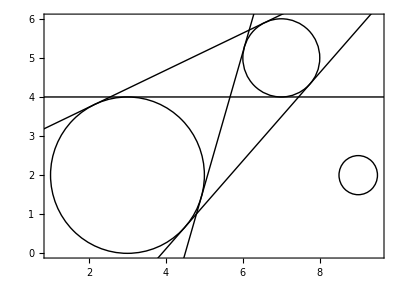

```mathematica
circle1={3,2,2};
circle2={7,5,1};
circle3={9,2,1/2};
Graphics[{
Circle[circle1[[1;;2]],circle1[[3]]],
Circle[circle2[[1;;2]],circle2[[3]]],
Circle[circle3[[1;;2]],circle3[[3]]]
}
~Join~circleCircleTangents[circle1[[1;;2]],circle1[[3]],circle2[[1;;2]],circle2[[3]]]
,Frame->True]
```

```mathematica
circleCircleTangents[circle1[[1;;2]],circle1[[3]],circle2[[1;;2]],circle2[[3]]]
```

{InfiniteLine[{{3,4},{7,4}}],InfiniteLine[{{123/25,36/25},{151/25,132/25}}],InfiniteLine[{{1/25 (83+12 √6),8/25 (7-2 √6)},{1/25 (179+6 √6),8/25 (16-√6)}}],InfiniteLine[{{1/25 (83-12 √6),8/25 (7+2 √6)},{1/25 (179-6 √6),8/25 (16+√6)}}]}

```mathematica
standardLineToInfiniteLine[{a_,b_,c_}]:=InfiniteLine[{0,-c/b},{b,-a}];
```

```mathematica
pointLineDistance[p_,{lA_,lB_,lC_}]:=RegionDistance[standardLineToInfiniteLine[{lA,lB,lC}],p];
```

```mathematica
locatorR=1;
Manipulate[
Graphics[{
Circle[{3,2},3],
Locator[Dynamic[locatorP]],
Circle[Dynamic[locatorP],locatorR]
}~Join~circleCircleTangents[{3,2},3,locatorP,locatorR]
,Frame->True,PlotRange->{{-2,15},{-2,15}}],
{{locatorP,{7,6}},Locator}
]
```